# Les B-Spline

Gérard Iglesias 
gerard_iglesias@mac.com

Surface B-Spline avec son polyèdre descripteur

## Introduction

Très utilisées dans le cadre des logiciels de création d'images, les splines constituent une primitive géométrique de base d'un nombre conséquent de logiciels de modélisation géométrique.

L'origine des splines remonte à l'utilisation, par les architectes et les dessinateurs industriels, de baguettes de bois ou de métal souple afin de tracer des courbes passant par un certain nombre de points caractéristiques.

Les courbes ainsi créées minimisent l'énergie de tension,et sont mathématiquement définies à l'aide de fonctions polynomiales par morceaux.

C'est ainsi que naturellement Mathematica offre des packages orientés calcul d'approximation et interpolation dont le résultat est une spline.

Dans le présent papier, je vais m'intéresser à une formulation plus visuelle et didactique qui vous permettra de mieux les appréhender et de jouer plus facilement avec leur représentation graphique 2D et 3D.

Les B-Splines permettent de définir des fonctions splines à l'aide d'une combinaison linéaire de fonctions de bases, la particularité étant que le lieu géométrique de la courbe ou surface ainsi obtenue est directement lié visuellement aux coefficients choisis, comme on peut le voir sur la figure .

Nous présenterons donc la définition des fonctions de bases, ensuite de simples combinaisons linéaires nous permettrons de jouer avec ces intéressants objets...

#### Notation

Les notations sont inspirées de l'ouvrage de Les Piegl et Wayne Tiller 'The NURBS Book'.

Pour une couverture générale du domaine des courbes et surfaces vous pourrez consulter le livre de Gerald Farin 'Curves and Surfaces for CAGD'.

Pour faciliter les notations nous allons définir l'accès à l'élément d'une liste ou d'une matrice grâce à la notation par indice

```mathematica
Subscript[U_List, i_Integer]:= U[[i+1]]
```

```mathematica
Subscript[P_List, i_Integer,j_Integer]:= P[[i+1]][[j+1]]
```

Le premier élément est par conséquent d’indice 0.

## Fonctions de base

Nous définissons la i-ème base B-spline 'N' de degré 'p' définit sur une série de réels croissants 'U' de la manière suivante :

```mathematica
Subscript[N, i_,0,U_][u_?NumberQ] := 1  /; Subscript[U, i] ≤u ∧ u < Subscript[U, i+1]
```

```mathematica
Subscript[N, i_,0,U_][u_?NumberQ] := 0  /; u < Subscript[U, i] ∨ Subscript[U, i+1] ≤ u
```

```mathematica
Subscript[N, i_,p_, U_][u_?NumberQ] := (u-Subscript[U, i])/(Subscript[U, i+p]-Subscript[U, i])Subscript[N, i,p-1,U][u] + (Subscript[U, i+p+1]-u)/(Subscript[U, i+p+1]-Subscript[U, i+1])Subscript[N, i+1,p-1,U][u] /; Subscript[U, i+p]≠Subscript[U, i]∧Subscript[U, i+p+1]≠Subscript[U, i+1]
```

```mathematica
Subscript[N, i_,p_, U_][u_?NumberQ] := (Subscript[U, i+p+1]-u)/(Subscript[U, i+p+1]-Subscript[U, i+1])Subscript[N, i+1,p-1,U][u] /; Subscript[U, i+p]==Subscript[U, i]∧ Subscript[U, i+p+1]≠Subscript[U, i+1]
```

```mathematica
Subscript[N, i_,p_, U_][u_?NumberQ] := (u-Subscript[U, i])/(Subscript[U, i+p]-Subscript[U, i])Subscript[N, i,p-1,U][u] /; Subscript[U, i+p]≠Subscript[U, i]∧Subscript[U, i+p+1]==Subscript[U, i+1]
```

```mathematica
Subscript[N, i_,p_, U_][u_?NumberQ] :=0 /; Subscript[U, i+p]==Subscript[U, i]∧Subscript[U, i+p+1]==Subscript[U, i+1]
```

### Exemple

Pour l'ensemble des fonctions splines de degré :

```mathematica
d = 3;
```

ayant pour support la série croissante de réels, que l'on appelle vecteur nœud' :

```mathematica
K = {0,0,0,0,1,2,3,3,3,4};
```

Le 'vecteur nœud' joue un rôle d'importance car il défini la longueur paramétrique des arc polynomiaux de la courbe à définir.

Ici j'ai utilisé une astuce: {....,3,3,3,4}, qui permet d'éviter une discontinuité en u=3, bien utile lors des évaluations numériques.

Les fonctions de base sont définies sur les supports successifs U_i U_(i+d+1)avec i∈{0,5}

Le tracé ne s'intéresse qu'à l'intervalle[0,3[car c'est l'intervalle pertinent pour les fonctions qui seront définies grâce à cette base.

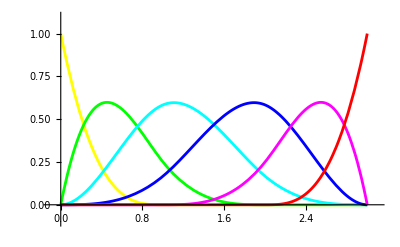

```mathematica
baseGR =
Plot[Evaluate[Table[Subscript[N, i,d,K][u], {i,0,5}]], {u,0,3},
PlotRange -> {{-0.1,3.1},{-0.1,1.1}},
PlotStyle->Table[{Hue[i/6], Dashing[{i/100, i/200}]}, {i,1,6}]]
```

## Fonction Spline

Exprimées sous forme de combinaison linéaire des fonctions de bases fourni une fonction polynomiale par morceaux définie sur intervalle [U_d, U_(Length[K]-d-1)[ :

```mathematica
Subscript[Bs, p_,U_,P_][u_] := ∑_(i=0)^(Length[U]-p-2) Subscript[N, i,p,U][u] Subscript[P, i]
```

### Exemple

```mathematica
P = {2,3,4,3.5,3,3.5}
```

{2,3,4,3.5,3,3.5}

Les bases ainsi définies entraîne une propriété géométrique intéressante, les coefficients extrêmes sont interpolées

```mathematica
{Subscript[Bs, d,K,P][0], Subscript[Bs, d,K,P][3]}
```

{2.,3.5}

Le tracé de la fonction correspondante sur l’intervalle [0,3]

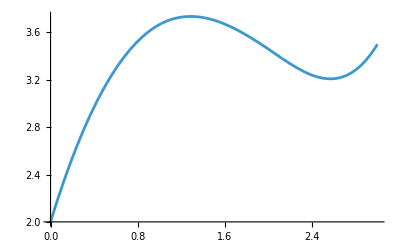

```mathematica
fonctionGR =
Plot[Subscript[Bs, d,K,P][u], {u,0,3}, PlotRange->All]
```

Nous obtenons le tracé combiné avec les fonctions de base:

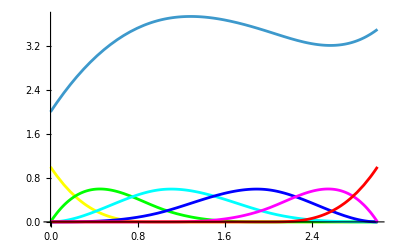

```mathematica
Show[{baseGR, fonctionGR},
PlotRange->All]
```

## Courbe paramétrique

Les splines deviennent vraiment intéressante lorsque elles sont utilisées pour décrire des courbes ou surface paramétriques, c'est à dire une ensemble de points du plan, ou de l'espace, dont chaque composante est une fonction B-Spline exprimé dans la même base de fonctions splines.

Pour une courbe paramétrique B-Spline dans l'espace R^n, dont les coefficients sont des points de l'espace R^nsous la forme : {{x_0, y_0, z_0}, {x_1, y_1, z_1}, ..., {x_(Length[K]-d-2), y_(Length[K]-d-2), z_(Length[K]-d-2)}}

Nous avons simplement la généralisation de l'expression des fonctions réelles :

```mathematica
Subscript[BsP, d_,U_,P_][u_]:=∑_(i=0)^(Length[U]-d-2) Subscript[N, i,d,U][u] Subscript[P, i]
```

### Exemples

#### Une courbe dans le plan

Les coordonnées dans le plan, que l'on nomme 'polygone descripteur' :

```mathematica
P2D = {{0,0},{0.2,4},{3,4},{3.5,20},{4,2},{6,0}};
```

Un tracé silencieux

```mathematica
polyGR = ParametricPlot[Subscript[BsP, d,K,P2D][u], {u, 0, 3},
DisplayFunction->Identity];
```

La combinaison avec le polygone descripteur :

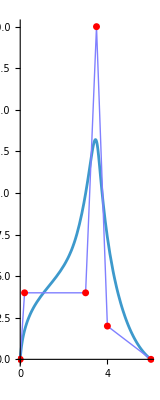

```mathematica
Show[{
polyGR,
Graphics[{RGBColor[0.5,0.5,1],Line[P2D],RGBColor[1,0,0],AbsolutePointSize[5],Map[Point[#]&,P2D]}]
},
PlotRange -> All,
DisplayFunction->$DisplayFunction
]
```

#### Une courbe dans l'espace

Simplement les coefficient sont définis dans l'espace:

```mathematica
P3D = 
{{0,0,0},{0,4,0.5},{4,4,1},{4,0,2},{0,0,2.5},{0,4,5}};
```

```mathematica
curve3DGR = ParametricPlot3D[Subscript[BsP, d,K,P3D][u], {u, 0, 3},
DisplayFunction->Identity]
```

-Graphics3D-

```mathematica
Show[
Graphics3D[{
RGBColor[0,0.5,0],Line[P3D],
RGBColor[0,0,1],PointSize[0.03],Map[Point, P3D],
RGBColor[1,0,0],Thickness[0.0075],curve3DGR[[1]]
}],
Axes ->True,
AxesLabel -> {"X", "Y", "Z"},
ViewPoint->{1.502, -2.415, 1.833}]
```

-Graphics3D-

## Surface paramétrique

Une surface paramétrique B-Spline est fonction de deux paramètres u et v, produit de chacune des 'directions' :

```mathematica
Subscript[BsS, du_,U_,dv_,V_,P_][u_,v_]:=∑_(i=0)^(Length[U]-du-2) ∑_(j=0)^(Length[V]-dv-2) Subscript[N, i,du,U][u]Subscript[N, j,dv,V][v] Subscript[P, i,j]
```

Les deux directions sont indépendant, elle peuvent avoir un degrés et un vecteur nœud différent...

### Exemple (la figure de la première page)

inclue le package Graphics3D pour le tracé de matrice de point obtenus par l'évaluation de la surface en (u,v) :

```mathematica
Poly3D ={
{{0,0,0},{0,1,0},{0,2,0},{0,3,0},{0,4,0}},{{1,0,0},{1,1,3},{1,2,3},{1,3,3},{1,4,0}},{{2,0,0},{2,1,3},{2,2,3},{2,3,3},{2,4,0}},{{3,0,0},{3,1,0},{3,2,0},{3,3,0},{3,4,0}},{{4,0,0},{4,1,0},{4,2,0},{4,3,0},{4,4,0}},{{5,0,0},{5,1,0},{5,2,0},{5,3,0},{5,4,0}}
};
```

```mathematica
Poly3DPoints = Table[Subscript[BsS, 3,{0,0,0,0,1,2,3,3,3,4},2,{0,0,0,1,2,3,3,4},Poly3D][u,v],
             {u,0,3,0.1},
             {v,0,3,0.1}];
surfaceGR = ParametricPlot3D[Subscript[BsS, 3,{0,0,0,0,1,2,3,3,3,4},2,{0,0,0,1,2,3,3,4},Poly3D][u,v], {u,0,3},
             {v,0,3}]
```

-Graphics3D-

```mathematica
Show[{
Graphics3D[{Thickness[0.005],Map[Line, Poly3D], Map[Line, Transpose[Poly3D]]}],
surfaceGR
},
ViewPoint->{0.934, -3.059, 1.104},
DisplayFunction -> $DisplayFunction]
```

-Graphics3D-